# Partícula en una caja

Objetivo : Analizar las funciones asociadas a la partícula en una caja.

Marco teórico: Solución de la ecuación de Schroedinger unidimensional cuando el potencial tiene la forma
V(x)=Piecewise[{{∞, x≤0}, {0, 0<x<L}, {∞, x≥L}}]
Para este caso las soluciones tienen la forma
ψ_n(x)=(2/L)^(1/2)sen(nπx/L) con n=1,2,..,∞

### Definición de las funciones propias

```mathematica
f[x_,n_,L_]:=Sqrt[2/L]*Sin[n*Pi*x/L];
```

Se puede verificar que estas funciones están normalizadas

```mathematica
Integrate[f[x,n,L]^2,{x,0,L}]
```

1-Sin[2 n π]/(2 n π)

El comportamiento de la función de onda en las fronteras se puede analizar evaluando la derivada de la función sobre x = 0 y x = L. Para n = 1

```mathematica
D[f[x,1,L],x]/.x->0
```

```mathematica
D[f[x,1,L],x]/.x->L
```

Para n = 2

```mathematica
D[f[x,2,L],x]/.x->0
```

```mathematica
D[f[x,2,L],x]/.x->L
```

Ejercicio 1 : Haga el análisis anterior para una n arbitraria y concluya sobre el valor de la derivada cuando se tiene una n par o una impar.

### Gráficas de las funciones y de las densidades de probabilidad para L=1

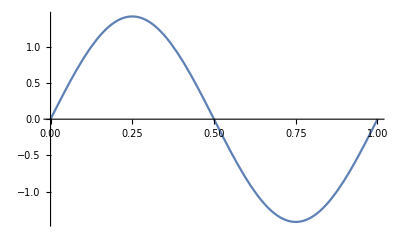

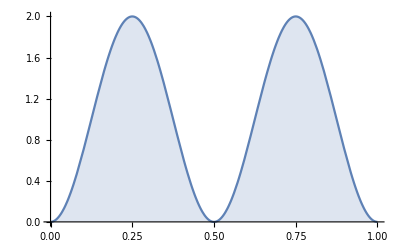

```mathematica
estado=2;
Plot[f[x,estado,1],{x,0,1}]
Plot[f[x,estado,1]*f[x,estado,1],{x,0,1},Filling->Axis]
```

### Cálculo de probabilidades

```mathematica
probabilidad[n_,a_,b_]:=Integrate[f[x,n,L]*f[x,n,L],{x,a,b},Assumptions->n∈Integers]
```

```mathematica
probabilidad[n,0,L/2]
```

```mathematica
Expand[%]
```

Ejercicio 2 : Hacer una análisis de la probabilidad de encontrar a la partícula en la región L/4 <= x <= 3 L/4. ¿Cuál es el resultado cuando n → ∞?

Solución :

```mathematica
probabilidad[n,L/4,3L/4]
```

```mathematica
Expand[%]
```

```mathematica
ListPlot[Table[probabilidad[n,L/4,3L/4],{n,1,40}],PlotJoined->True]
```

```mathematica
Limit[probabilidad[n,L/4,3L/4],n->Infinity]
```

### Evaluación de la energía cinética

```mathematica
ecinetica[n_]:=Integrate[f[x,n,L]*(-ℏ^2)*D[f[x,n,L],{x,2}]/(2*m),{x,0,L}];
```

```mathematica
ecinetica[n]
```

```mathematica
Expand[%]
```

### Definición de los valores esperados de la posición y el momento lineal

```mathematica
promx[n_]:=Integrate[f[x,n,L]*x*f[x,n,L],{x,0,L}];
promxcuad[n_]:=Integrate[f[x,n,L]*x^2*f[x,n,L],{x,0,L}];
prompx[n_]:=Integrate[f[x,n,L]*ℏ*D[f[x,n,L],x]/I,{x,0,L}];
prompxcuad[n_]:=Integrate[f[x,n,L]*ℏ^2*D[f[x,n,L],{x,2}]/(I*I),{x,0,L}];
```

```mathematica
Expand[prompxcuad[n]]
```

```mathematica
Expand[promx[n]]
```

```mathematica
prompx[n]
```

### Evaluación de la desviación cuadrática media de la posición y el momento

```mathematica
deltax[n_]:=Sqrt[promxcuad[n]-promx[n]^2]
```

```mathematica
deltapx[n_]:=Sqrt[prompxcuad[n]-prompx[n]^2]
```

```mathematica
deltax[1]*deltapx[1]
```

```mathematica
Simplify[%]//N
```

### Análisis en dos dimensiones

```mathematica
solucion2D[x_,y_,nx_,ny_,Lx_,Ly_]:=f[x,nx,Lx]f[y,ny,Ly];
```

```mathematica
Lx=1;Ly=1;
nx=3;ny=1;
g1=Plot3D[solucion2D[x,y,nx,ny,Lx,Ly],{x,0,Lx},{y,0,Ly},Boxed->False,Axes->False];
g2=Plot3D[solucion2D[x,y,nx,ny,Lx,Ly]^2,{x,0,Lx},{y,0,Ly},Boxed->False,Axes->False];
Clear[Lx,Ly,nx,ny];
```

```mathematica
energia[nx_,ny_,a_]=Simplify[-(h/(2m))(D[solucion2D[x,y,nx,ny,a,a],{x,2}]+D[solucion2D[x,y,nx,ny,a,a],{y,2}])/solucion2D[x,y,nx,ny,a,a]]
```

```mathematica
energia[1,1,a]
```

```mathematica
energia[1,2,a]
```

```mathematica
relativa[nx_,ny_,a_]:=energia[nx,ny,a]/energia[1,1,a]
```

```mathematica
relativa[1,2,a]
```

```mathematica
Plot3D[relativa[nx,ny,a],{nx,1,10},{ny,1,10}]
```

### Efecto tunel

En este caso una partícula con energía E impacta una barrera de potencial de ancho L y altura V. En nuestro caso analizaremos las situaciones donde la energía de la partícula es menor a la altura de la barrera, como lo muestra la siguiente gráfica:

```mathematica
pot[x_]:=0/;x<0
pot[x_]:=altura/;x≥0&&x≤longitud
pot[x_]:=0/;x>longitud
altura=3;longitud=2;energia=1;
etiqueta1=Text["Energía",{-5,energia+0.1}];
etiqueta2=Text["Potencial",{1.5,altura+.2}];
g1=Plot[pot[x],{x,-10,10},PlotRange->{0,4},Filling->Bottom];
g2=Plot[energia,{x,-10,10},PlotRange->{0,4}];
Show[g1,g2,Graphics[etiqueta1],Graphics[etiqueta2]]
Clear[altura, longitud, energia];
```

La función de onda se escribe en tres regiones. La región I (x < 0) contiene la descripción de una onda incidente y una que se refleja al golpear la barrera de altura V. En esta región E < V. La región II (0 <= x <= L) contiene la descripción de la partícula en la región E < V y la región III (x > L) representa la onda que se llega a transmitir.

```mathematica
funcizq[x_]:=A*Exp[I*k*x]+B*Exp[-I*k*x]
```

```mathematica
funcdentro[x_]:=C*Exp[kapa*x]+D*Exp[-kapa*x]
```

```mathematica
funcder[x_]:=AP*Exp[I*k*x]
```

Imponiendo la continuidad en la función de onda y en su primer derivada en x = 0

```mathematica
uno=Solve[{funcizq[0]==funcdentro[0],(D[funcizq[x],x]/.x->0)==(D[funcdentro[x],x]/.x->0)},{C,D}]
```

Ahora imponemos la misma condición a la anterior para x = L

```mathematica
dos=Solve[{funcdentro[L]==funcder[L],(D[funcdentro[x],x]/.x->L)==(D[funcder[x],x]/.x->L)},{C,D}]
```

Finalmente se despeja a la constante B

```mathematica
tres=Solve[(C/.uno[[1]])==(C/.dos[[1]]),B]
```

```mathematica
cuatro=Solve[(D/.uno[[1]])==(D/.dos[[1]]),B]
```

Resolviendo para los coeficientes A y AP

```mathematica
solucion=Solve[(Expand[(B/.tres[[1]])/AP])==(Expand[(B/.cuatro[[1]])/AP]),{A,AP}]
```

```mathematica
cuadrado=Simplify[Conjugate[(AP/.solucion[[1]])/A]*((AP/.solucion[[1]])/A),Assumptions->Im[k]==0&&Im[kapa]==0&&Im[L]==0]
```

El resultado se escribe en términos de m, h, L, E y V

```mathematica
transmision=Simplify[cuadrado/.k->Sqrt[2*m*ener]/h/.kapa->Sqrt[2*m*(altura-ener)]/h]
```

Hagamos experimentos variando m, L y V

```mathematica
m=.1;h=1;L=.1;altura=2;
Plot[transmision,{ener,0,altura},PlotRange->{0,1}]
```

```mathematica
nx=2;ny=2;nz=1;
lx=ly=lz=1.0;
g1=DensityPlot3D[(2/lz)^(1/2)(2/ly)^(1/2)(2/lx)^(1/2)Sin[nx x Pi/lx] Sin[ny y Pi/ly]Sin[nz z Pi/lz],{x,0,lx},{y,0,ly},{z,0,lz},OpacityFunction->Interval[{0.0,.08}],Boxed->False,Axes->False];
SliceDensityPlot3D[Sin[nx x Pi/lx] Sin[ny y Pi/ly]Sin[nz z Pi/lz],{x,0,lx},{y,0,ly},{z,0,lz}];
g2=SliceContourPlot3D[Sin[nx x Pi/lx] Sin[ny y Pi/ly]Sin[nz z Pi/lz],{x,0,lx},{y,0,ly},{z,0,lz},Contours->20,Boxed->False,Axes->False];
g3=ContourPlot3D[{Sin[nx x Pi/lx] Sin[ny y Pi/ly]Sin[nz z Pi/lz]==0.3,Sin[nx x Pi/lx] Sin[ny y Pi/ly]Sin[nz z Pi/lz]==-0.3},{x,0,lx},{y,0,ly},{z,0,lz},Boxed->False,Axes->False];
```

```mathematica
?SliceContourPlot3D
```